Kitaev Random Circuit |

Setting up the modelpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#516853239 | Analysispaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1487900726
Simulationpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1068023573 |

Here, the effects of random measurements on the entanglement in the Kitaev chain of Majorana fermions is investigated. A realization of such Kitaev random circuit is shown in Figure 1.

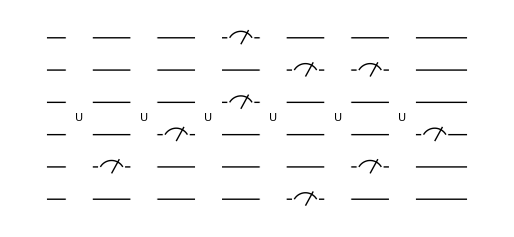

Figure 1. A typical form of Kitaev random circuit. Each line indicates a fermion mode, the unitary gate with label U denotes the time-evolution of Kitaev's model of Majorana fermions, and the measurement symbols depict the measurement of occupation number of the fermion modes.

NambuStatepaclet:Q3/ref/NambuStateQ3 Package Symbol | Represents a many-fermion quantum state for non-interacting fermions with pairing correlation
NambuUnitarypaclet:Q3/ref/NambuUnitaryQ3 Package Symbol | Unitary gate associated with a Bogoliubov-de Gennes type Hamiltonian
NambuOperatorpaclet:Q3/ref/NambuOperatorQ3 Package Symbol | Non-unitary gate on BdG states
RandomWickCircuitSimulatepaclet:Q3/ref/RandomWickCircuitSimulateQ3 Package Symbol | Rancomd quantum circuit consisting of fermionic gates.
WickGreenFunctionpaclet:Q3/ref/WickGreenFunctionQ3 Package Symbol | Calculates the Green's functions with respect to a Wick state
WickEntanglementEntropypaclet:Q3/ref/WickEntanglementEntropyQ3 Package Symbol | Calculates the entanglement entropy in a Wick state
WickLogarithmicNegativitypaclet:Q3/ref/WickLogarithmicNegativityQ3 Package Symbol | Calculates the logarithmic negativity in a Wick state

Functions for fermionic quantum computation.

Make sure to load Q3.

```mathematica
<<Q3`
```

This document requires the recent version of Q3.

```mathematica
Q3Assure["3.5.12"]
```

Setting up the model

The bare fermion modes.

```mathematica
Let[Fermion,c]
```

Consider a system of n fermion modes.

```mathematica
$n=6;
cc=c[Range@$n]
cccc=Join[cc,Dagger@cc];
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6)}

Construct the many-body Hamiltonian of the Kitaev chain (Kitaev, 2001)https://doi.org/10.1070/1063-7869/44/10S/S29.

```mathematica
HH=-Q[cc]-t*PlusDagger[Hop@cc]+Δ*PlusDagger[Pair@cc]//Garner
```

-Graphics-

Examine the connectivity between neighboring fermion modes.

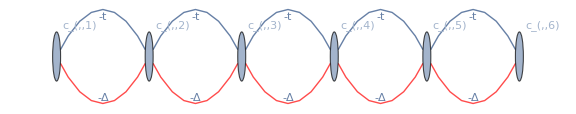

```mathematica
GraphForm[HH]
```

Extract the single-particle (or Bogoliubov-de Gennes) Hamiltonian (cf. many-body Hamiltonian in the above) of the model in the Nambu space.

```mathematica
barH=CoefficientTensor[HH,Dagger@cccc,cccc];
ArrayShort[barH,"Size"->8]
```

(-1/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2 | …
-t/2 | -1/2 | -t/2 | 0 | 0 | 0 | Δ/2 | 0 | …
0 | -t/2 | -1/2 | -t/2 | 0 | 0 | 0 | Δ/2 | …
0 | 0 | -t/2 | -1/2 | -t/2 | 0 | 0 | 0 | …
0 | 0 | 0 | -t/2 | -1/2 | -t/2 | 0 | 0 | …
0 | 0 | 0 | 0 | -t/2 | -1/2 | 0 | 0 | …
0 | Δ/2 | 0 | 0 | 0 | 0 | 1/2 | t/2 | …
-Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | t/2 | 1/2 | …
… | … | … | … | … | … | … | … | …)

The time interval for each unitary layer to operate.

```mathematica
$τ=0.5;
```

Construct the single-particle unitary matrix in the Nambu space. Recall the convention:
	c̲ ↦U̲ c̲  with (c̲)^†:=(c_1,…,c_n,c_1^†,…,c_n^†) and  U̲:=(U | V
V^* | U^*).

```mathematica
barU=MatrixExp[-I*$τ*Normal[barH]/.{t->1,Δ->1}];
PartitionInto[barU,{1,2}]//ArrayShort
```

((0.908981+0.237213 ⅈ | -0.0599369+0.232165 ⅈ | 0.000633605-0.00501574 ⅈ | -2.65865×10^-6+0.000031737 ⅈ | …
-0.0599369+0.232165 ⅈ | 0.849041+0.22715 ⅈ | -0.0593032+0.232229 ⅈ | 0.000630946-0.00501593 ⅈ | …
0.000633605-0.00501574 ⅈ | -0.0593032+0.232229 ⅈ | 0.849039+0.227149 ⅈ | -0.0593032+0.232229 ⅈ | …
-2.65865×10^-6+0.000031737 ⅈ | 0.000630946-0.00501593 ⅈ | -0.0593032+0.232229 ⅈ | 0.849039+0.227149 ⅈ | …
… | … | … | … | …) | (0.0605731 | -0.000636269+0.237213 ⅈ | 2.66461×10^-6-0.00504757 ⅈ | -5.96735×10^-9+0.0000318322 ⅈ | …
-0.000636269-0.237213 ⅈ | 2.66461×10^-6 | -5.96735×10^-9+0.237213 ⅈ | 0.-0.00504757 ⅈ | …
2.66461×10^-6+0.00504757 ⅈ | -5.96735×10^-9-0.237213 ⅈ | 0 | 0.+0.237213 ⅈ | …
-5.96735×10^-9-0.0000318322 ⅈ | 0.+0.00504757 ⅈ | 0.-0.237213 ⅈ | 0 | …
… | … | … | … | …))

Construct the corresponding unitary operator. It has the same information as the above unitary matrix, but operates directly on Wick states.

```mathematica
wu=NambuUnitary[barU,cc]
```

NambuUnitary[…]

Prepare an initial state. A half-filling is a common choice.

```mathematica
in=Ket[cc->PadRight[{1,0},$n,{1,0}]]
in=NambuState[in]
```

1_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))0_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))

NambuState[…]

The probability to perform a measurement on each fermion mode.

```mathematica
$p=.2;
```

The depth of quantum circuit.

```mathematica
$T=6; (* must be an integer *)
```

Simulation

The simulation involves a lot of random number generators. To get the same result every time you open this document, set the seed of the random number generator.

```mathematica
SeedRandom[354];(*for tests*)
```

Construct 10 random circuits and run each circuit 5 times. Notice the "Samples"→{10,5} option.

```mathematica
EchoTiming[
{data,qc}=RandomWickCircuitSimulate[cc,in,wu,$p,$T,"Samples"->{10,5}];
]
```

0.531947

Examine the output data format: There are 10 entries because the same number of quantum circuits were randomly generated.

```mathematica
Length[qc]
```

10

```mathematica
Dimensions[data]
```

{10,5,13}

If you want, examine the circuits by displaying them in a graphical form.

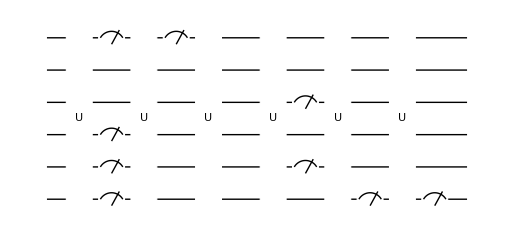

```mathematica
Show[qc[[2]]]
```

Examine some of the output states as well.

```mathematica
out=data[[2,2,3]]
```

NambuState[…]

```mathematica
Elaborate[out]//Chop
```

0.968879 1_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))0_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))-(4.65011×10^-8-0.247535 ⅈ) 1_(,,c_(,,1))1_(,,c_(,,2))0_(,,c_(,,3))0_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))

Analysis

Each entry in the converted data wcs contains the information about one realization of quantum trajectory. Extract the trajectory history in an explicit form, for example, of the first entry.

```mathematica
trj=Flatten[data,1];
```

In this particular case, there are 13 entries; the first entry is just the initial state and the rest are corresponds to the layers; there are 6 layers and each layer contains two sublayers of unitary evolution and measurements.

```mathematica
Dimensions[trj]
```

{50,13}

Note that the output states are all normalized.

```mathematica
EchoTiming[nrm=Map[NormSquare,trj,{2}];]
ArrayShort[nrm]
```

0.18223

(1. | 1. | 1. | 1. | …
1. | 1. | 1. | 1. | …
1. | 1. | 1. | 1. | …
1. | 1. | 1. | 1. | …
… | … | … | … | …)

```mathematica
DeleteCases[Flatten@nrm//IntegerChop,1]
```

{}

For further analysis, take the subsystem. Below, we will consider entanglement properties between this subsystem and the rest.

```mathematica
aa=Take[cc,Floor[$n/2]]
```

{c_(,,1),c_(,,2),c_(,,3)}

### Entanglement Entropy

Recall that in this particular example, there are 50 trajectories; and 13 Wick states along each trajectory.

```mathematica
Dimensions[trj]
```

{50,13}

Again, the subsystem has a half of the whole modes.

```mathematica
aa=Take[cc,Floor[$n/2]]
```

{c_(,,1),c_(,,2),c_(,,3)}

Calculate the entanglement entropy.

```mathematica
EchoTiming[ee=Map[WickEntanglementEntropy[#,aa]&,trj,{2}];]
```

2.16886

Take the average of the entanglement entropy over different trajectories, and plot it as a function of time.

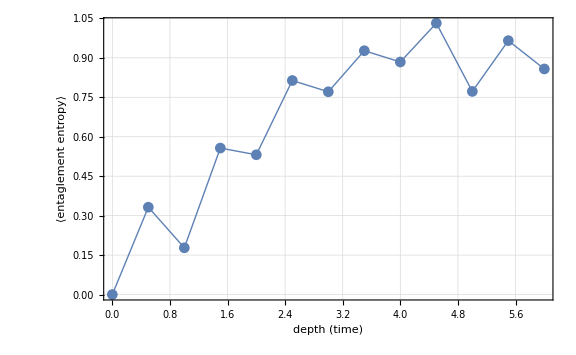

```mathematica
ListLinePlot[Mean[ee],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "⟨entaglement entropy⟩"}]
```

### Logarithmic Negativity

For further analysis, take the subsystem. This has been defined above; just in case.

```mathematica
aa=Take[cc,Floor[$n/2]];
```

At the moment, the current implementation of WickLogarithmicNegativity does not handle trivial cases of Green’s function, which internally lead to singular matrices. To avoid such cases, put a small value to the “Epsilon” option.

```mathematica
SetOptions[WickLogarithmicNegativity,"Epsilon"->1.25*^-5]
```

{Epsilon→0.0000125}

Calculate the logarithmic negativity of each state in the particular trajectory.

```mathematica
EchoTiming[neg=Map[WickLogarithmicNegativity[aa],trj,{2}];]
```

9.00592

Plot the entanglement (logarithmic negativity) of the first trajectory.

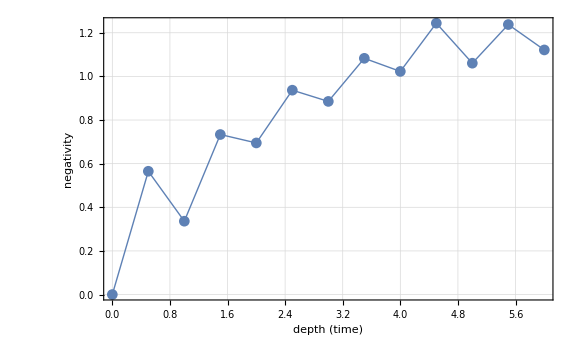

```mathematica
ListLinePlot[Mean[Re@neg],
PlotRange->All,
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "negativity"}]
```

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪B. M. Terhal and D. P. DiVincenzo (2002)https://doi.org/10.1103/PhysRevA.65.032325, Physical Review A 65, 032325, "Classical simulation of noninteracting-fermion quantum circuits."
▪A. Yu. Kitaev (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, Physics-Uspekhi 44, 131 (2001), "Unpaired Majorana fermions in quantum wires." 
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
▪About Q3